InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

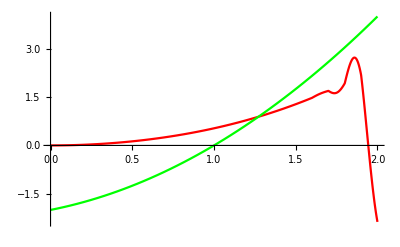

(R | p | Am | E | E+1/r | Al
1 | 1.27171 | 0.888942 | -3.23447 | -2.23447 | 0.888942)

```mathematica
(* Matrix Dimensions *)
(* From HydrogenIon-2D-6.tex  *) 

Get["/Users/zelimir/Work/Physics-Thesis/thesis-2/MathematicaCode/FindRootsMultiple.m"];

(* Mathieu's eigenvalues, Even and Odd 
Input parameters: p - values of p for which we calculate A
         n - order of the continuous fraction
		  evenOdd - flag to choose even or odd Mathieu's function *)
eigenM[p_,n_Integer,  evenOdd_Integer]:=Module[{w,q,v, A, mCoeffV0, mCoeffV1,rez},
w:=-A +p^2/2.;      q:= -p^2/4.;
v[nn_]:=(w-nn^2)/q;
mCoeffV0[nn_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,nn}]];
mCoeffV1[nn_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,nn}]];

rez =If[EvenQ[evenOdd],
	NSolve[SetPrecision[mCoeffV0[n]==0,Infinity],{A},Reals],
	NSolve[SetPrecision[mCoeffV1[n]==0,Infinity],{A},Reals]];
rez = Sort[A  /. rez, Abs[#2]> Abs[#1]&];
rez[[1]]
];

(* Create L Matrix 
 Input parameters:    
	    dim - matrix dimensions 
      R - distance betwen nuclei *)
makeLMatrix[dim_, R_]:=Module[{matrix, d,lSum},
d[m_,n_]:=KroneckerDelta[m,n];
	
lSum[m_,n_] =(-p^2-p + n +2R)d[m,n]+ n d[n+1,m];
 
matrix = Table[Table[(-1)lSum[m,n],{n,0,dim-1}],
{m,0,dim-1}
];
matrix
];



(* Calculate eigenvalues of the M equation 
 Parameters:     pRange - list of all p.
             R - distance between nuclei
              n - order of the continuous fracition
              index - i-th eigenvalue, 1,2,3..
             evenOdd - flag to choose even or odd Mathieu's function *)
calcMEigenvalues[pRange_List, R_, n_Integer,evenOdd_Integer] := Module[{data,a},
data=Map[(a = eigenM[#,n,evenOdd];{#,a}) &, pRange];
data
];

(* Eigenvalues from the L equation 
 Parameters:     pRange - list of all p.
             R - distance between nuclei
              n - order of the continuous fracition
              index - i-th eigenvalue  1,2,3...*)
          
calcLEigenvalues[pRange_List,R_,dim_Integer, index_Integer]:=Module[{matrixL,eigenData,a},
matrixL = makeLMatrix[dim,R] ;
eigenData  = Map[(a = Sort[Select[ Eigenvalues[N[matrixL/.p->#, 40]],Im[#]==0.&], Greater][[index]]; {#,a}) &, pRange];
eigenData
];

(* Calculate electron energy for a given R 
 R - distance between nuclei *)
calcEnergy[R_, index_Integer,evenOdd_Integer]:=Module[
{pRange = Range[0.1,5,.1], nM= 4, nL= 40,
eigenMValues, eigenLValues,mFunc, lFunc,p, ee, am, al, root},

(* returns {p,A} *)
eigenMValues= calcMEigenvalues[pRange, R,nM, evenOdd];
eigenLValues = calcLEigenvalues[pRange, R, nL,index];

       mFunc = Interpolation[eigenMValues, InterpolationOrder->6];
lFunc  =Interpolation[ eigenLValues, InterpolationOrder->6];

p = x /.FindRoot[mFunc[x] == lFunc[x],{x,1}];
(*p= x /. SortBy[FindRoot[mFunc[x] == lFunc[x],{x, 0,2}], Last];*)

Print[Plot[{mFunc[x],lFunc[x]},{x,0,2}, PlotStyle->{Red,Green}]];

(* values of A  *)
am= mFunc[p];
al= lFunc[p];
ee = -2(p/R)^2;
{R, p, am, ee, ee + 1/R, al}
];

allRs = Table[0.1+i*0.1,{i,0,9}];
allRs = Join[allRs, Table[1+.5*i,{i,1,16}]];

outValsEven0= Map[calcEnergy[#1,1,0] &,{1}];

(*outValsEven1= Map[calcEnergy[#1,2,0] &,{1}];*)

Prepend[outValsEven0,{"R","p", "Am","E","E+1/r","Al"}] // MatrixForm
```